# Arm model

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]

cm=72/2.54;
figExpPath="/Users/thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/";
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->9}];
```

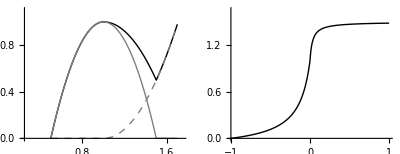

/Users/thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/muscle.eps

```mathematica
min = 0.25;
max = 1.75;
ratio = 0.8;

lp=1.0;
kp=0.5/(1.5-lp)^2;

Fl[l_] := If[l>0.5&&l<1.5,1-((l-1)/0.5)^2,0];
Fp [l_]:=If[l>lp,kp(l-lp)^2,0];

flpl=Plot[Fl[l],{l,0.5,1.7},PlotRange->{{min,max},{0,1.1}},AxesOrigin->{min,0},PlotStyle->Gray];

fppl=Plot[Fp[l],{l,0.5,1.7},PlotRange->{{min,max},{0,1.1}},AxesOrigin->{min,0},PlotStyle->{Gray,Dashed}];

fspl=Plot[Fl[l]+Fp[l],{l,0.5,1.7},PlotRange->{{min,max},{0,1.1}},AxesOrigin->{min,0},PlotStyle->{Black}];

flpl=Show[fspl,flpl,fppl,AspectRatio->ratio];
hillSh=0.15;
hillLn=0.15;
hillMax=1.5;
hillSlope=2.0;
hillSub=(hillLn/hillSlope)*((1-hillMax)/(1+hillLn));

Fvc[v_]:=(1+v)/(1-v/hillSh);
Fve[v_]:=(hillSub-hillMax*v)/(-v+hillSub);
Fv[v_]:=If[v<0,Fvc[v],Fve[v]];

fvpl=Plot[Fv[v],{v,-1,1},AspectRatio->ratio,PlotRange->{{-1,1},{0,1.1*hillMax}},AxesOrigin->{-1,0},PlotStyle->Black];
fpl =GraphicsRow[{flpl,fvpl},ImageSize->400]
Export[figExpPath<>"muscle.eps",Show[fpl,ImageSize->8.9cm],ImageSize->8.9cm]
```

```mathematica
Flv[a_,l_,v_]:=a*Fl[l]*Fv[v]+Fp[l];

r1=Range[0.5,1.7,0.05];
r2=Range[-1,1,0.1];
c1=PadLeft[{},Length[r1],Black];
c2=PadLeft[{},Length[r2],Black];
rc1=Transpose[{r1,c1}];
rc2=Transpose[{r2,c2}];

rc1= Join[rc1,{{1,Directive[Thick,Red]}}];
rc2= Join[rc2,{{0,Directive[Thick,Red]}}];

light={White};
style=None;
mesh={ rc1,rc2};
view=2*{-0.5,-2,1};

PlotSurface[a_]:=Plot3D[Flv[a,l,v],{l,0.5,1.7},{v,-1,1},Mesh->mesh,BoundaryStyle->Black,Boxed->True,Lighting->light,PlotStyle->style,ViewPoint->view,BoxRatios->{1,1,0.5},PlotRange->{{0.5,1.7},{-1,1},{0,1.1*hillMax}}];

PlotSurface[1]

p=GraphicsGrid[Partition[Table[PlotSurface[a],{a,0.5,1,0.5}],2],ImageSize->8.9cm]
Export[figExpPath<>"surface.eps",Show[p,ImageSize->8.9cm],ImageSize->8.9cm]
```

-Graphics3D-

-Graphics-

/Users/thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/surface.eps